```mathematica
$Assumptions=i∈Integers && j ∈ Integers && i >=1 && j >=1&&l[i]>0&&xe>0&&l[i]<xe&&l[j]>0&&l[j]<xe&&i<j&&l[i]<l[j]
```

i∈ℤ&&j∈ℤ&&i≥1&&j≥1&&l[i]>0&&xe>0&&l[i]<xe&&l[j]>0&&l[j]<xe&&i<j&&l[i]<l[j]

```mathematica
Φ[i_,x_]:=Sin[i Pi x]
Subscript[Φ, e][i_,x_]:=Piecewise[{{α[i]x,0<=x<1-l[i]/xe},{α[i] (xe/l[i]-1)(1- x),1-l[i]/xe<=x<1}}]
```

```mathematica
D[Subscript[Φ, e][i,x],{x}]
```

Piecewise[{{α[i], x≥0&&x+l[i]/xe<1}, {-((-1+xe/l[i]) α[i]), x+l[i]/xe≥1&&x<1}, {0, True}}]

```mathematica
int1=Integrate[Subscript[Φ, e][i,x]Subscript[Φ, e][i,x],{x,0,1}]//FullSimplify
Solve[int1==1/2,α[i]]
Integrate[Φ[i,x]Φ[i,x],{x,0,1}]
```

((xe-l[i])^2 α[i]^2)/(3 xe^2)

{{α[i]→ConditionalExpression[-(√(3/2) xe)/(√(xe^2-2 xe l[i]+l[i]^2)), xe-l[i]≠0]},{α[i]→ConditionalExpression[(√(3/2) xe)/(√(xe^2-2 xe l[i]+l[i]^2)), xe-l[i]≠0]}}

1/2

```mathematica
Integrate[Subscript[Φ, e][i,x],{x,0,1}]
```

(xe α[i]-l[i] α[i])/(2 xe)

```mathematica
Integrate[Φ[j,x]Φ[j,x],{x,0,1}]
Integrate[Φ[i,x]Φ[j,x],{x,0,1}]
```

1/2

0

```mathematica
Integrate[Φ[i,x]Subscript[Φ, e][j,x],{x,0,1}]//FullSimplify
```

((-1)^(1+i) xe Sin[(i π l[j])/xe] α[j])/(i^2 π^2 l[j])

```mathematica
Integrate[Subscript[Φ, e][i,x]Subscript[Φ, e][j,x],{x,0,1}]//FullSimplify
```

((xe-l[j]) (-l[i]^2+(2 xe-l[j]) l[j]) α[i] α[j])/(6 xe^2 l[j])

```mathematica
Integrate[D[Φ[j,x], x]D[Φ[j,x], x],{x,0,1}]
Integrate[D[Φ[i,x], x]D[Φ[j,x], x],{x,0,1}]
```

(j^2 π^2)/2

0

```mathematica
Integrate[D[Φ[i,x], x]D[Subscript[Φ, e][j,x], x],{x,0,1}]//FullSimplify
```

((-1)^(1+i) xe Sin[(i π l[j])/xe] α[j])/l[j]

```mathematica
Integrate[D[Subscript[Φ, e][i,x], x]D[Subscript[Φ, e][j,x], x],{x,0,1}]//FullSimplify
```

((xe-l[j]) α[i] α[j])/l[j]

```mathematica
Integrate[D[Subscript[Φ, e][i,x], x]D[Subscript[Φ, e][i,x], x],{x,0,1}]//FullSimplify
```

((xe-l[i]) α[i]^2)/l[i]

```mathematica
Integrate[x D[Φ[i,x], x],{x,0,1}]
```

(-1+(-1)^i)/(i π)

```mathematica
Integrate[x D[Subscript[Φ, e][i,x], x],{x,0,1}]
```

-((xe-l[i]) α[i])/(2 xe)

```mathematica
Integrate[x^2 D[Φ[i,x], x,x],{x,0,1}]
```

(2-2 (-1)^i+(-1)^i i^2 π^2)/(i π)

```mathematica
Integrate[x^2 D[Subscript[Φ, e][i,x], x,x],{x,0,1}]
```

0

```mathematica
Integrate[x D[Φ[i,x], x] Φ[j,x],{x,0,1}]
Integrate[x D[Φ[i,x], x] Φ[i,x],{x,0,1}]
```

((-1)^(i+j) i j)/(i^2-j^2)

-1/4

```mathematica
Integrate[x D[Φ[i,x], x] Subscript[Φ, e][j,x],{x,0,1}]//FullSimplify
```

1/(i^2 π^2 l[j])(-1)^i (i π (-1+Cos[(i π l[j])/xe]) (xe-l[j])+2 xe Sin[(i π l[j])/xe]) α[j]

```mathematica
Integrate[x D[Subscript[Φ, e][i,x], x] Φ[j,x],{x,0,1}]//FullSimplify
```

((-1)^(1+j) (j π (-1+Cos[(j π l[i])/xe]) (xe-l[i])+xe Sin[(j π l[i])/xe]) α[i])/(j^2 π^2 l[i])

```mathematica
r1=Integrate[x D[Subscript[Φ, e][i,x], x] Subscript[Φ, e][j,x],{x,0,1}]//FullSimplify
r1/.{j->i}//FullSimplify
```

((xe-l[j]) (-3 xe l[i]+2 l[i]^2+(2 xe-l[j]) l[j]) α[i] α[j])/(6 xe^2 l[j])

-((xe-l[i])^2 α[i]^2)/(6 xe^2)

```mathematica
Integrate[x D[Subscript[Φ, e][i,x], x] Subscript[Φ, e][i,x],{x,0,1}]//FullSimplify
```

-((xe-l[i])^2 α[i]^2)/(6 xe^2)

```mathematica
Integrate[x^2 D[Φ[i,x], x,x]Φ[i,x],{x,0,1}]//FullSimplify
Integrate[x^2 D[Φ[i,x], x,x]Φ[j,x],{x,0,1}]//FullSimplify
```

1/4-(i^2 π^2)/6

-(4 (-1)^(i+j) i^3 j)/((i^2-j^2)^2)

```mathematica
Integrate[x^2 D[Φ[i,x], x,x]Subscript[Φ, e][j,x],{x,0,1}]//FullSimplify
```

1/(i^2 π^2 xe l[j])(-1)^i (-4 i π xe (-1+Cos[(i π l[j])/xe]) (xe-l[j])+((-6+i^2 π^2) xe^2+i^2 π^2 l[j] (-2 xe+l[j])) Sin[(i π l[j])/xe]) α[j]

```mathematica
Integrate[x^2 D[Subscript[Φ, e][i,x], x,x]Φ[j,x],{x,0,1}]//FullSimplify
```

0

```mathematica
Integrate[x^2 D[Subscript[Φ, e][i,x], x,x]Subscript[Φ, e][j,x],{x,0,1}]//FullSimplify
```

0

```mathematica
Integrate[D[Φ[i,x], x,x]Φ[i,x],{x,0,1}]//FullSimplify
Integrate[D[Φ[i,x], x,x]Φ[j,x],{x,0,1}]//FullSimplify
```

-1/2 i^2 π^2

0

```mathematica
Integrate[ D[Φ[i,x], x,x]Subscript[Φ, e][j,x],{x,0,1}]//FullSimplify
```

((-1)^i xe Sin[(i π l[j])/xe] α[j])/l[j]

```mathematica
Integrate[ D[Subscript[Φ, e][i,x], x,x]Φ[j,x],{x,0,1}]//FullSimplify
Integrate[ D[Subscript[Φ, e][i,x], x,x]Subscript[Φ, e][j,x],{x,0,1}]//FullSimplify
```

0

0

```mathematica
Integrate[D[Φ[i,x], x,x]  Φ[i,x],{x,0,1}]/.{α[i]->Sqrt[3/2] xe/(xe-l[i])}//FullSimplify
```

-1/2 i^2 π^2

```mathematica
Integrate[Subscript[Φ, e][i,x]Subscript[Φ, e][j,x],{x,0,1}]
```

((xe-l[j]) (-l[i]^2+2 xe l[j]-l[j]^2) α[i] α[j])/(6 xe^2 l[j])

```mathematica
Integrate[Subscript[Φ, e][i,x]Subscript[Φ, e][j,x],{x,0,1}]//Simplify
```

((xe-l[j]) (-l[i]^2+(2 xe-l[j]) l[j]) α[i] α[j])/(6 xe^2 l[j])

```mathematica
Subscript[Φ, e][i,x]
```

Piecewise[{{x α[i], 0≤x<1-l[i]/xe}, {(1-x) (-1+xe/l[i]) α[i], 1-l[i]/xe≤x<1}, {0, True}}]

```mathematica
cond={α[i]->1,α[j]->2,l[i]->0.1xe,l[j]->0.2xe}
```

{α[i]→1,α[j]→2,l[i]→0.1 xe,l[j]→0.2 xe}

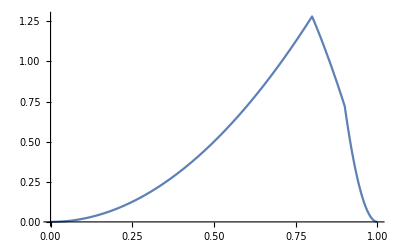

```mathematica
Plot[Subscript[Φ, e][i,x] Subscript[Φ, e][j,x]/.cond,{x,0,1}]
```

```mathematica
sol=Integrate[Subscript[Φ, e][i,x] Subscript[Φ, e][j,x],{x,0,1}]//Simplify
```

((xe-l[j]) (-l[i]^2+(2 xe-l[j]) l[j]) α[i] α[j])/(6 xe^2 l[j])

```mathematica
((xe-l[j]) (-l[i]^2+(2 xe-l[j]) l[j]) α[i] α[j])/(6 xe^2 l[j])/.cond
```

0.466667

```mathematica
Integrate[Subscript[Φ, e][i,x] Subscript[Φ, e][j,x],{x,0,1}]/.cond
```

0.466667

```mathematica
Integrate[Subscript[Φ, e][j,x] Subscript[Φ, e][i,x]/.cond,{x,0,1}]
```

0.466667